# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Spin transport\\Quantum channel\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14];
```

# Ising chaometer

```mathematica
J=1;
h=1.05;
L=8;
g=0.5;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[J,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,allvecs},DistributedContexts->Full];
```

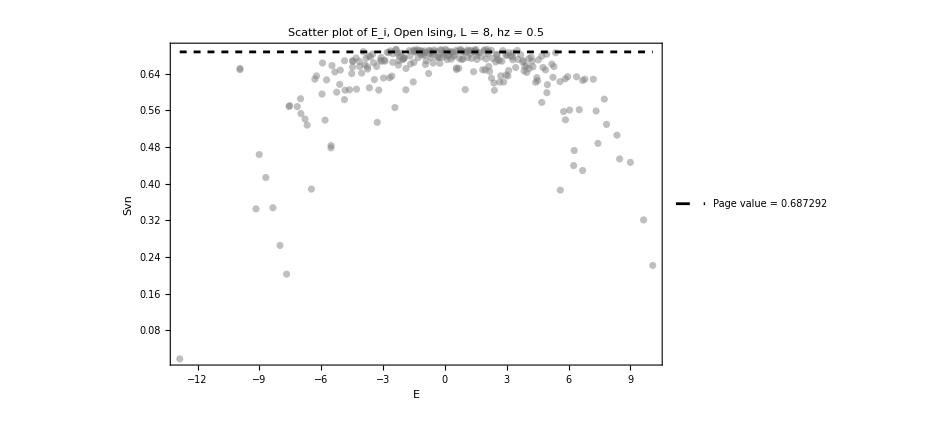

```mathematica
Show[{ListPlot[Transpose[{allvals,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[g]<>"",25,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],10];
(*productstate2=Table[Flatten[KroneckerProduct[haar[1],haar[L-1]]],50];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,productstate2},DistributedContexts->Full];
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;5]][[All,3]];
```

```mathematica
tlist=Table[i,{i,0,200,0.05}];
tlist//Length
```

4001

```mathematica
fakesvn=Table[ParallelTable[{t,pur[L,La,Lb,i,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

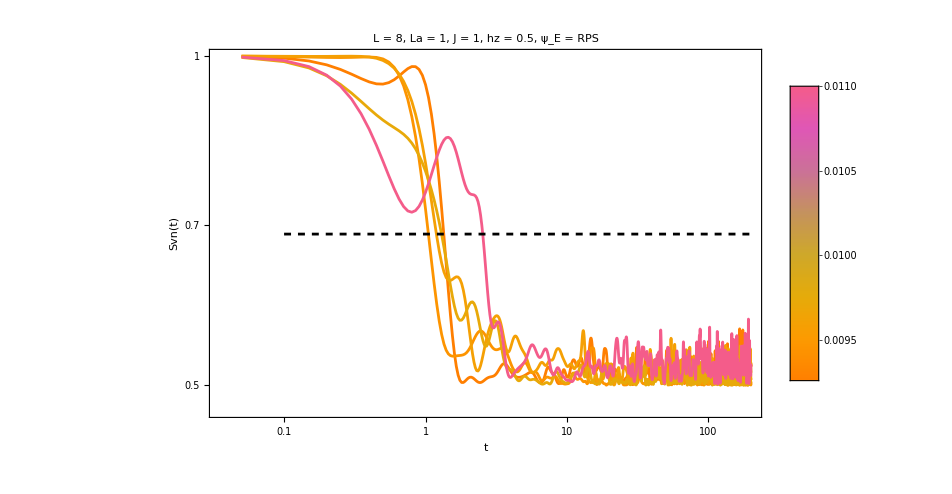

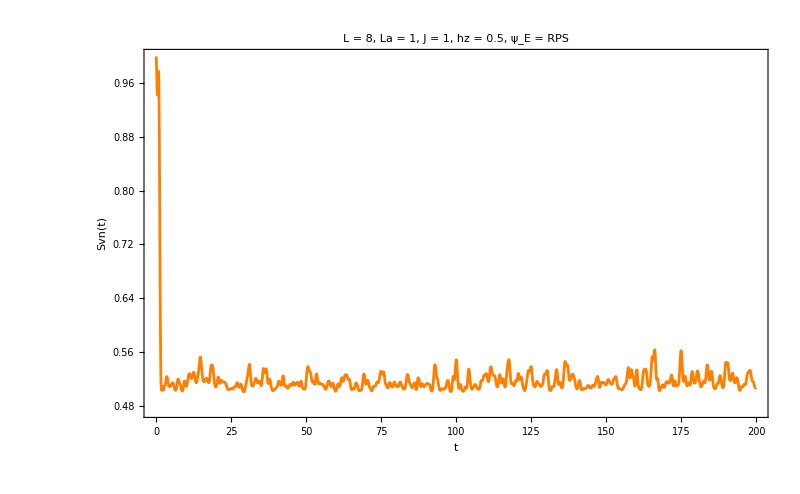

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;5]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLogPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->25],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->800,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLogPlot[pageEntropy[La,Lb],{x,10^-1,Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
i=1;
ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",25,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->800,PlotStyle->Directive[colorMapping[sorted[[i]]]]]
```

# Choi matrix ising

## Test old

```mathematica
i=1;
ψ=productstate[[i]];
rho=Chop[MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}]];
```

```mathematica
{L,La,Lb}
ψ//Dimensions
rho//Dimensions
```

{5,1,4}

{32}

{16,16}

```mathematica
A=KroneckerProduct[IdentityMatrix[2^(Lb)]/2^(La),rho];
P=Transpose[allvecs];
Pinv=Conjugate[allvecs];
```

```mathematica
A//Dimensions
allvecs//Dimensions
```

{256,256}

{32,32}

```mathematica
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*allvals*t]].Pinv;
```

```mathematica
AbsoluteTiming[chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist}];
truepurity=Chop[Map[Tr,Map[#.#&,chois]]];]
```

{12.0477,Null}

```mathematica
chois[[1]]//Dimensions
```

{4,4}

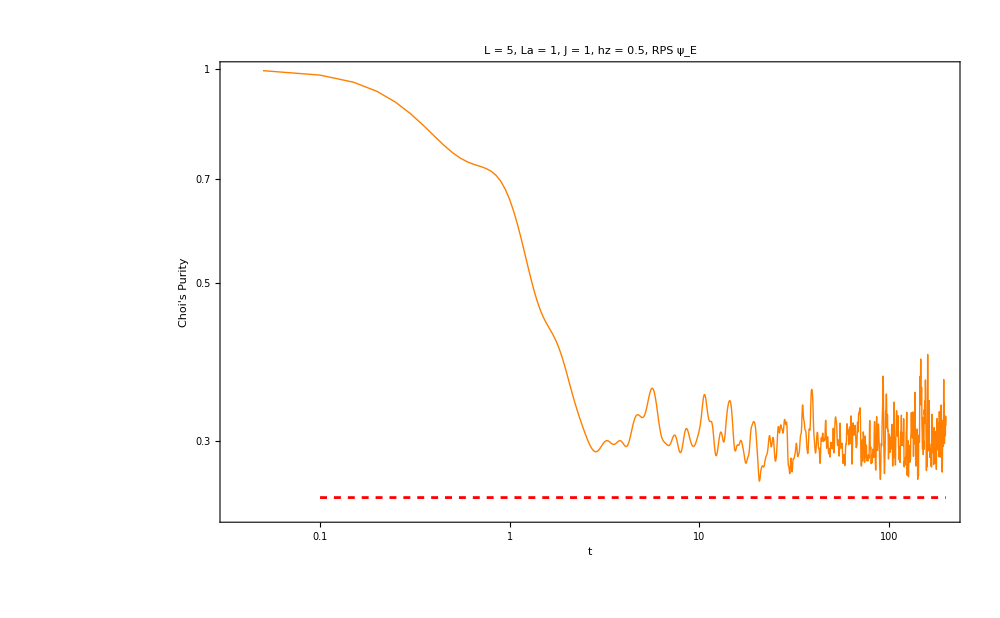

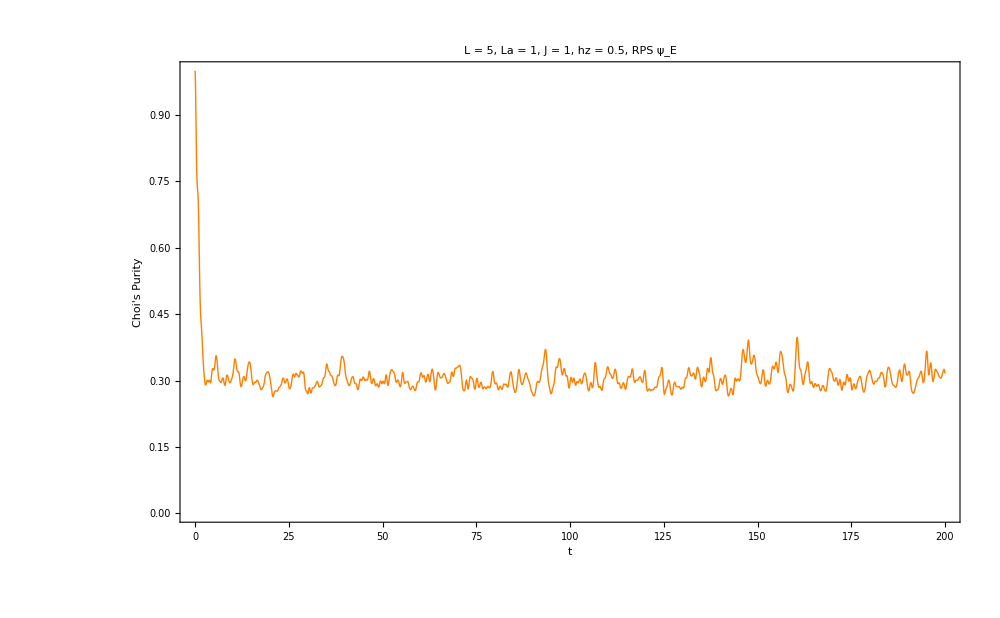

0.307297

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]];
final=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}]
ListPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]]
decoherence[truepurity,tlist]
```

## Improved code c

```mathematica
Needs["Developer`"];
ClearAll[PackC];
PackC[x_]:=Developer`ToPackedArray[x];
(*1) Environment state from a global pure state|ψ⟩ on S⊗E*)
ClearAll[EnvStateFromPsi];
EnvStateFromPsi[psi_,m_Integer?Positive,n_Integer?Positive]:=PackC@Chop@MatrixPartialTrace[Dyad[psi],1,{m,n}];
(*2) Fast spectral unitary builder:U(t)=V.diag(e^{-i λ t}).V^†,implemented via column scaling (no DiagonalMatrix allocation)*)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_,allvals_]:=Module[{P=PackC@Transpose[allvecs],Pinv=PackC@Conjugate[allvecs]},Function[{t},With[{ph=PackC@Exp[-I allvals t]},PackC@(Transpose[Transpose[P]*ph].Pinv)]]];
ClearAll[PhiProjector];
PhiProjector[m_Integer?Positive]:=Module[{phi=PackC@(Flatten[IdentityMatrix[m]]/Sqrt[m])},PackC@Dyad[phi]];
ClearAll[ChoiSysBuilder];
Options[ChoiSysBuilder]={"rhoE"->None,"psi"->None};
ChoiSysBuilder[m_Integer?Positive,n_Integer?Positive,unitaryF_Function,opts:OptionsPattern[]]:=Module[{rhoE=OptionValue["rhoE"],psi=OptionValue["psi"],projPhi,idm},If[rhoE===None&&psi===None,Message[ChoiSysBuilder::envspec];Return[$Failed]];
If[rhoE=!=None&&psi=!=None,Message[ChoiSysBuilder::envboth];Return[$Failed]];
rhoE=If[rhoE===None,EnvStateFromPsi[psi,m,n],rhoE]//PackC;
projPhi=PhiProjector[m];
idm=IdentityMatrix[m,SparseArray];(*sparse identity*)Function[{t},Module[{U=unitaryF[t],UR,Omega,X},UR=KroneckerProduct[idm,U];(*acts on R⊗S⊗E*)Omega=KroneckerProduct[projPhi,rhoE];(* |Φ⟩⟨Φ|⊗ρE*)X=UR.Omega.ConjugateTranspose[UR];
PackC@Chop@MatrixPartialTrace[X,3,{m,m,n}]]]];

ChoiSysBuilder::envspec="Provide either \"rhoE\" -> (n×n matrix) or \"psi\" -> (mn-vector).";
ChoiSysBuilder::envboth="Provide only one of \"rhoE\" or \"psi\", not both.";

ClearAll[ProcessPurity];
Options[ProcessPurity]={"Parallel"->True};
ProcessPurity[choiF_Function,tlist_List,OptionsPattern[]]:=Module[{par=TrueQ[OptionValue["Parallel"]]},If[par,ParallelMap[(Chop@Re@Tr[#.#])&@*choiF,tlist,Method->"CoarsestGrained"],Map[(Chop@Re@Tr[#.#])&@*choiF,tlist]]];
```

```mathematica
m=2^La;
n=2^Lb;
i=1;
ψ=productstate[[i]];
(*Option A:environment given as a pure global state|ψ⟩*)
rhoE=EnvStateFromPsi[ψ,m,n];
unitaryF=SpectralUnitary[allvecs,allvals];
choiF=ChoiSysBuilder[m,n,unitaryF,"rhoE"->rhoE];
```

```mathematica
(*Purity over your tlist*)
AbsoluteTiming[purity=ProcessPurity[choiF,tlist];]
```

{329.35,Null}

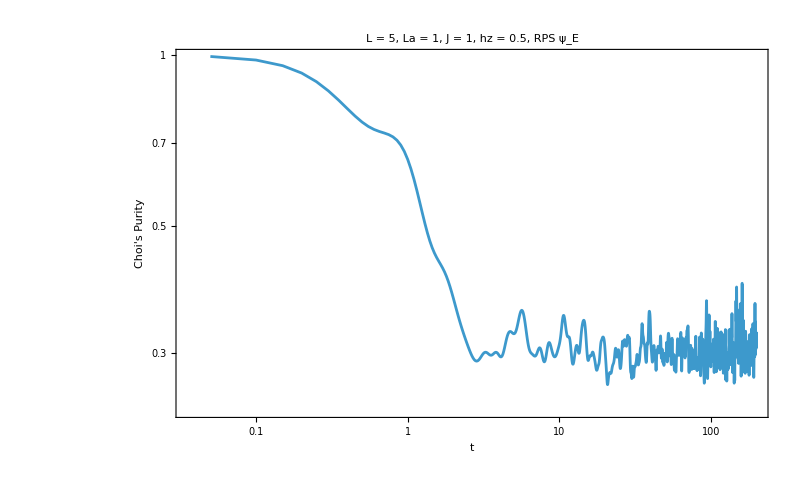

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```

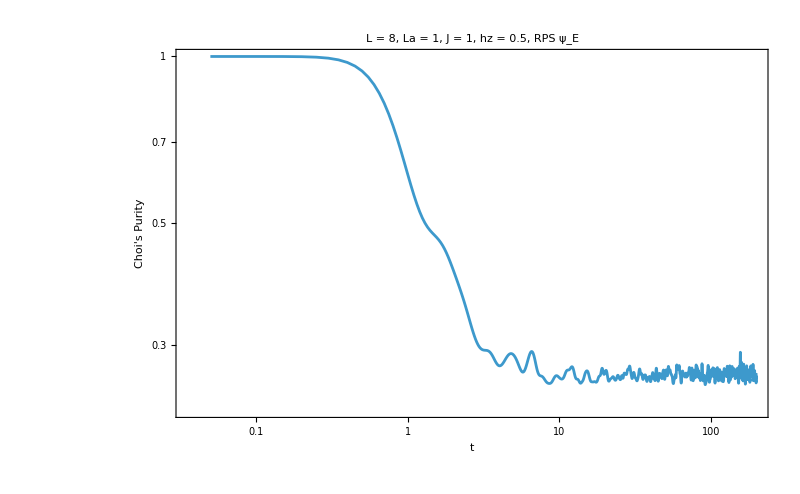

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```

# Spin chain, pure states

```mathematica
J=1;
h=1.05;
L=5;
g=0.;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[J,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
(*Spin 1*)
H1[Δa_]:=Δa*Pauli[3];
(*Spin 2*)
H2[Δb_]:=Δb*Pauli[3];
```

```mathematica
Clear[Hlocal];
Hlocal[Δa_,Δb_]:=KroneckerProduct[H1[Δa],IdentityMatrix[2^L],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],Ha,IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2^L],H2[Δb]];
```

```mathematica
Pauliplus=PauliMatrix[1]+I*PauliMatrix[2];
Pauliminus=PauliMatrix[1]-I*PauliMatrix[2];
```

```mathematica
(*Spin 1 coupling*)
H1c[λa_]:=λa*(KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]+ConjugateTranspose[KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]]);
(*Spin 2*)
H2c[λb_]:=λb*(KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]+ConjugateTranspose[KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]]);
```

```mathematica
Clear[HT];
HT[Δa_,Δb_,λa_,λb_]:=Hlocal[Δa,Δb]+H1c[λa]+H2c[λb];
```

```mathematica
initialchain=RandomChainProductState[L];
initialchain=coherentstate[qubit[0,0],L];
initialspin1=RandomChainProductState[1];
initialspin2=RandomChainProductState[1];
initial=Flatten[KroneckerProduct[initialspin1,initialchain,initialspin2]];
```

```mathematica
{Δa,Δb,λa,λb}={1,1,1,1};
```

```mathematica
{fullval,fullvec}=Transpose[Sort[Transpose[Eigensystem[HT[Δa,Δb,λa,λb]]]]];
```

```mathematica
tlist=Table[i,{i,0,10,0.1}];
```

```mathematica
stateevolved=ParallelTable[StateEvolution[t,initial,fullval,fullvec],{t,tlist},DistributedContexts->Full];
```

```mathematica
survival=ParallelTable[Abs[Conjugate[initial].i]^2,{i,stateevolved}];
```

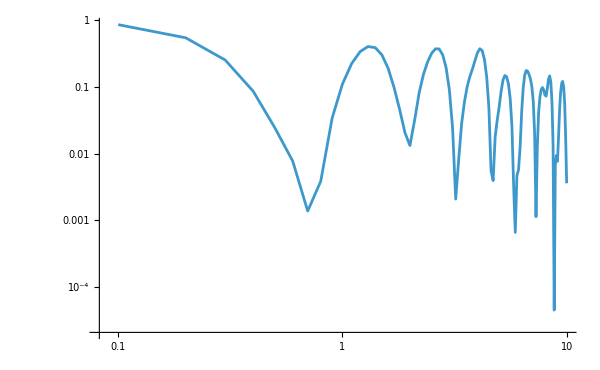

```mathematica
ListLogLogPlot[Transpose[{tlist,survival}],PlotRange->All,Joined->True,ImageSize->600]
```

## Subsystem evolution

```mathematica
rhoevolved=ParallelTable[Chop[MatrixPartialTrace[Dyad[i],{2,3},{2,2^L,2}]],{i,stateevolved},DistributedContexts->Full];
puritya=ParallelTable[Chop[Tr[i.i]],{i,rhoevolved}];
```

```mathematica
rhoevolved=ParallelTable[Chop[MatrixPartialTrace[Dyad[i],{2},{2,2^L,2}]],{i,stateevolved},DistributedContexts->Full];
purityb=ParallelTable[Chop[Tr[i.i]],{i,rhoevolved}];
```

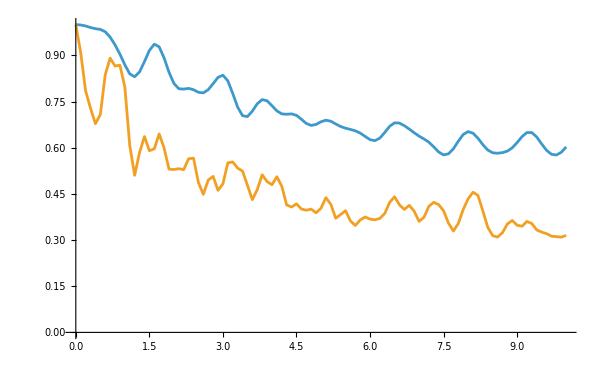

```mathematica
ListPlot[{Transpose[{tlist,puritya}],Transpose[{tlist,purityb}]},PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
ClearAll[VNentropy]
VNentropy[0 | 0.] = 0;
VNentropy[x_] := -x*Log[x];
```

```mathematica
(* Calculate entropy for every time step *)
entropyList = Table[Total[VNentropy /@ Chop[Eigenvalues[rho]]],{rho, rhoevolved}];
```

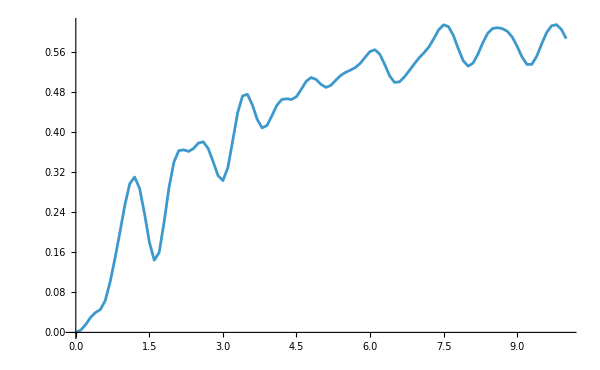

```mathematica
ListPlot[Transpose[{tlist,entropyList}],PlotRange->All,Joined->True,ImageSize->600]
```

# Spin chain

```mathematica
J=1;
h=1.05;
L=5;
g=0.1;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[J,g,J,L,BoundaryConditions->"Open"];
(*system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];*)
```

```mathematica
(*Spin 1*)
H1[Δa_]:=Δa*Pauli[3];
(*Spin 2*)
H2[Δb_]:=Δb*Pauli[3];
```

```mathematica
Clear[Hlocal];
Hlocal[Δa_,Δb_]:=KroneckerProduct[H1[Δa],IdentityMatrix[2^L],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],Ha,IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2^L],H2[Δb]];
```

```mathematica
Pauliplus=PauliMatrix[1]+I*PauliMatrix[2];
Pauliminus=PauliMatrix[1]-I*PauliMatrix[2];
```

```mathematica
(*Spin 1 coupling*)
H1c[λa_]:=λa*(KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]+ConjugateTranspose[KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]]);
(*Spin 2*)
H2c[λb_]:=λb*(KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]+ConjugateTranspose[KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]]);
```

```mathematica
Clear[HT];
HT[Δa_,Δb_,λa_,λb_]:=Hlocal[Δa,Δb]+H1c[λa]+H2c[λb];
```

```mathematica
(* 1. Setup states exactly as you have them *)
bellState = 1/Sqrt[2]*{1, 0, 0, 1};
rho12 = Dyad[bellState];
rhochain = Dyad[coherentstate[qubit[1., 0], L]];
(* 2. Build temporary matrix in [Q1, Q2, Chain] order *)
tempInitial = KroneckerProduct[rho12, rhochain];
```

```mathematica
(* Assume 'rhoGeneral' is your arbitrary, correlated (4*2^L) x (4*2^L) matrix *)
(* Layout of rhoGeneral is [Q1, Q2, Chain] *)
dimC = 2^L;
(* but calculate the position of that state in the old [q1, q2, c] layout *)
permList = Flatten[Table[
    q1 * (2^(L + 1)) + q2 * (2^L) + c + 1, 
    {q1, 0, 1}, {c, 0, dimC - 1}, {q2, 0, 1}
]];
(* Transform the general matrix into your physical layout [Q1, Chain, Q2] *)
initial = tempInitial[[permList, permList]];
```

```mathematica
{Δa,Δb,λa,λb}={1,1,1,1};
```

```mathematica
{fullval,fullvec}=Transpose[Sort[Transpose[Eigensystem[HT[Δa,Δb,λa,λb]]]]];
```

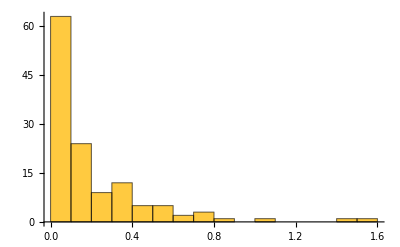

```mathematica
Histogram[Differences[Sort[fullval]]]
```

```mathematica
tlist=Table[i,{i,0,100,0.1}];
```

```mathematica
ClearAll[DensityMatrixEvolution];
DensityMatrixEvolution[t_, rho0_, eigenvals_, eigenvecs_] := 
 Module[{rhoEnergy, phaseMatrix, rhoEnergyT},
rhoEnergy = eigenvecs . rho0 . ConjugateTranspose[eigenvecs];
phaseMatrix = Table[Exp[-I * (m - n) * t], {m, eigenvals}, {n, eigenvals}];
rhoEnergyT = rhoEnergy * phaseMatrix;
Chop[ConjugateTranspose[eigenvecs].rhoEnergyT.eigenvecs]
]
```

```mathematica
ClearAll[Survivalrho]
Survivalrho[rho0_, rhot_] := Module[{sqrtRho0},
  (* Check if rho0 is pure to use the faster standard trace method *)
  If[Chop[Tr[rho0 . rho0]] >= 0.999,
   Chop[Tr[rho0 . rhot]], 
   (* Otherwise, use the full mixed-state Uhlmann fidelity definition *)
   sqrtRho0 = MatrixPower[rho0, 1/2];
   Chop[Tr[MatrixPower[sqrtRho0 . rhot . sqrtRho0, 1/2]]]^2
  ]
]
```

```mathematica
(* Run the full matrix evolution loop *)
globalEvolutionData = ParallelTable[
   Module[{rhoGlobal, surv,rhoReduced},
rhoGlobal=DensityMatrixEvolution[t, initial,fullval,fullvec];
   (* 2. Compute global survival probability *)
    surv = Survivalrho[initial, rhoGlobal];    
    (* 3. Compute the reduced 4x4 density matrix for your spins *)
    rhoReduced = Chop[MatrixPartialTrace[rhoGlobal, {2}, {2, 2^L, 2}]];    
    (* Return everything in a structured association for easy access *)
    <|"Time" -> t, "Survival" -> surv, "RhoReduced" -> rhoReduced|>
   ],
   {t, tlist},
   DistributedContexts -> Full
];
```

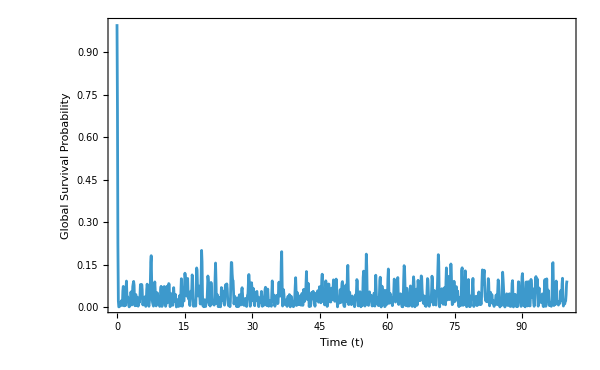

```mathematica
ListLinePlot[Table[{d["Time"],d["Survival"]},{d,globalEvolutionData}],PlotRange->All,Frame->True,FrameLabel->{"Time (t)","Global Survival Probability"},ImageSize->600]
```

## Subsystem evolution

```mathematica
(* Evolve the full density matrix and isolate ONLY Spin 1 *)
rhoevolved = ParallelTable[
     Module[{rhoGlobal},
rhoGlobal = DensityMatrixEvolution[t, initial, fullval, fullvec];Chop[MatrixPartialTrace[rhoGlobal, {2, 3}, {2, 2^L, 2}]]
     ], 
     {t, tlist}, 
     DistributedContexts -> Full
   ];
```

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,rhoevolved}];
```

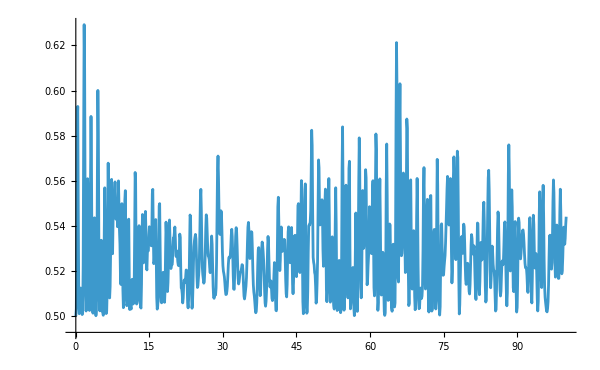

```mathematica
ListPlot[Transpose[{tlist,purity}],PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
ClearAll[VNentropy]
VNentropy[0 | 0.] = 0;
VNentropy[x_] := -x*Log[x];
```

```mathematica
(* Calculate entropy for every time step *)
entropyList = Table[Total[VNentropy /@ Chop[Eigenvalues[rho]]],{rho, rhoevolved}];
```

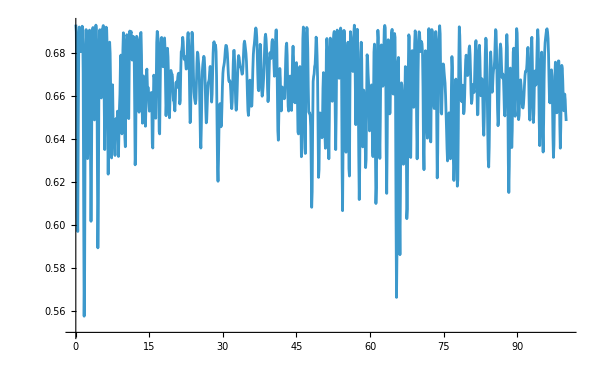

```mathematica
ListPlot[Transpose[{tlist,entropyList}],PlotRange->All,Joined->True,ImageSize->600]
```

# Spin chain Ising generalizing

## Setup

```mathematica
L=5;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
(*Spin 1*)
H1[Δa_]:=Δa*Pauli[3];
(*Spin 2*)
H2[Δb_]:=Δb*Pauli[3];
Pauliplus=PauliMatrix[1]+I*PauliMatrix[2];
Pauliminus=PauliMatrix[1]-I*PauliMatrix[2];
```

```mathematica
(*Spin 1 coupling*)
H1c[λa_]:=λa*(KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]+ConjugateTranspose[KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]]);
(*Spin 2*)
H2c[λb_]:=λb*(KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]+ConjugateTranspose[KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]]);
```

```mathematica
ClearAll[DensityMatrixEvolution];
DensityMatrixEvolution[t_, rho0_, eigenvals_, eigenvecs_] := 
 Module[{rhoEnergy, phaseMatrix, rhoEnergyT},
rhoEnergy = eigenvecs . rho0 . ConjugateTranspose[eigenvecs];
phaseMatrix = Table[Exp[-I * (m - n) * t], {m, eigenvals}, {n, eigenvals}];
rhoEnergyT = rhoEnergy * phaseMatrix;
Chop[ConjugateTranspose[eigenvecs].rhoEnergyT.eigenvecs]
]
```

```mathematica
ClearAll[Survivalrho]
Survivalrho[rho0_, rhot_] := Module[{sqrtRho0},
  (* Check if rho0 is pure to use the faster standard trace method *)
  If[Chop[Tr[rho0 . rho0]] >= 0.999,
   Chop[Tr[rho0 . rhot]], 
   (* Otherwise, use the full mixed-state Uhlmann fidelity definition *)
   sqrtRho0 = MatrixPower[rho0, 1/2];
   Chop[Tr[MatrixPower[sqrtRho0 . rhot . sqrtRho0, 1/2]]]^2
  ]
]
```

```mathematica
ClearAll[VNentropy]
VNentropy[0 | 0.] = 0;
VNentropy[x_] := -x*Log[x];
```

## Parameters

```mathematica
J=1;
h=1.05;
g=0.;
```

```mathematica
Ha=IsingHamiltonian[J,g,J,L,BoundaryConditions->"Open"];
```

```mathematica
Clear[Hlocal];
Hlocal[Δa_,Δb_]:=KroneckerProduct[H1[Δa],IdentityMatrix[2^L],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],Ha,IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2^L],H2[Δb]];
```

```mathematica
Clear[HT];
HT[Δa_,Δb_,λa_,λb_]:=Hlocal[Δa,Δb]+H1c[λa]+H2c[λb];
```

```mathematica
(* 1. Setup states exactly as you have them *)
bellState = 1/Sqrt[2]*{1, 0, 0, 1};
rho12 = Dyad[bellState];
rhochain = Dyad[RandomChainProductState[L]];
rhochain = Dyad[coherentstate[qubit[0., 0], L]];
tempInitial = KroneckerProduct[rho12, rhochain];
```

```mathematica
(* Layout of tempInitial is [Q1, Q2, Chain] *)
dimC = 2^L;
(* but calculate the position of that state in the old [q1, q2, c] layout *)
permList = Flatten[Table[
    q1 * (2^(L + 1)) + q2 * (2^L) + c + 1, 
    {q1, 0, 1}, {c, 0, dimC - 1}, {q2, 0, 1}
]];
(* Transform the general matrix into your physical layout [Q1, Chain, Q2] *)
initial = tempInitial[[permList, permList]];
```

```mathematica
initialchain=RandomChainProductState[L];
initialspin1=RandomChainProductState[0];
initialspin2=RandomChainProductState[1];
initial=Flatten[KroneckerProduct[initialspin1,initialchain,initialspin2]];
initial=Dyad[initial];
```

## Method

```mathematica
{Δa,Δb,λa,λb}={1,1,0.35,0.35};
```

```mathematica
{fullval,fullvec}=Transpose[Sort[Transpose[Eigensystem[HT[Δa,Δb,λa,λb]]]]];
```

```mathematica
MeanLevelSpacingRatio[Sort[fullval]]
```

0.368129

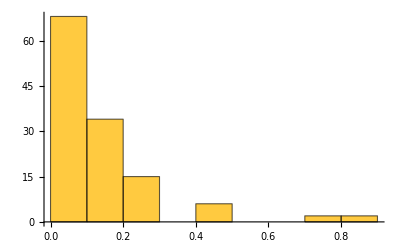

```mathematica
Histogram[Differences[Sort[fullval]],PlotRange->All]
```

```mathematica
tlist=Table[i,{i,0,20,0.05}];
```

```mathematica
(* Run the full matrix evolution loop *)
globalEvolutionData = ParallelTable[
   Module[{rhoGlobal, surv,rhoReduced},
rhoGlobal=DensityMatrixEvolution[t, initial,fullval,fullvec];
   (* 2. Compute global survival probability *)
    surv = Survivalrho[initial, rhoGlobal];    
    (* 3. Compute the reduced 4x4 density matrix for your spins *)
    rhoReduced = Chop[MatrixPartialTrace[rhoGlobal, {2}, {2, 2^L, 2}]];    
    (* Return everything in a structured association for easy access *)
    <|"Time" -> t, "Survival" -> surv, "RhoReduced" -> rhoReduced|>
   ],
   {t, tlist},
   DistributedContexts -> Full
];
```

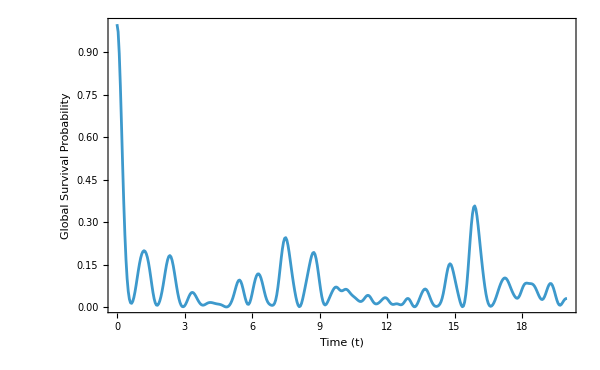

```mathematica
ListLinePlot[Table[{d["Time"],d["Survival"]},{d,globalEvolutionData}],PlotRange->All,Frame->True,FrameLabel->{"Time (t)","Global Survival Probability"},ImageSize->600]
```

## Subsystem evolution

```mathematica
(* Evolve the full density matrix and isolate ONLY Spin 1 *)
rhoevolved = ParallelTable[
     Module[{rhoGlobal},
rhoGlobal = DensityMatrixEvolution[t, initial, fullval, fullvec];Chop[MatrixPartialTrace[rhoGlobal, {2, 3}, {2, 2^L, 2}]]
     ], 
     {t, tlist}, 
     DistributedContexts -> Full
   ];
```

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,rhoevolved}];
```

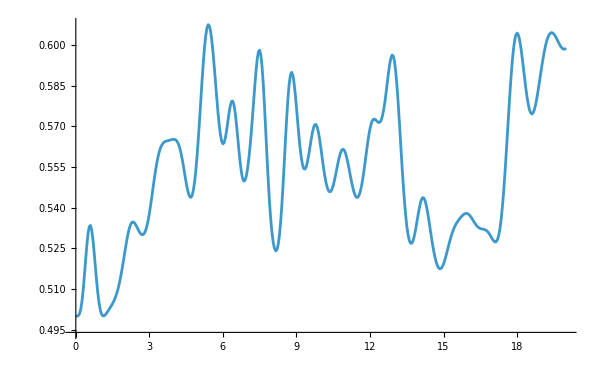

```mathematica
ListPlot[Transpose[{tlist,purity}],PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
(* Calculate entropy for every time step *)
entropyList = Table[Total[VNentropy /@ Chop[Eigenvalues[rho]]],{rho, rhoevolved}];
```

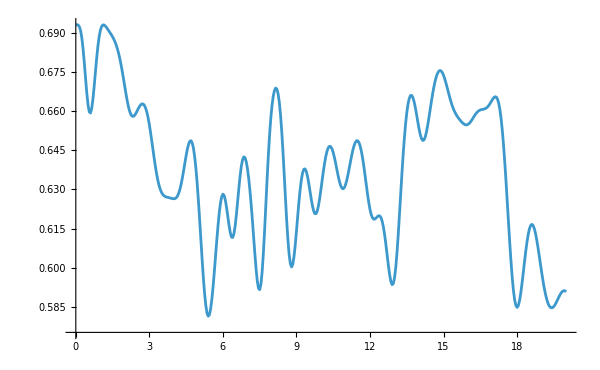

```mathematica
ListPlot[Transpose[{tlist,entropyList}],PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
(* Ensure the function is defined just in case *)
ClearAll[SurvivalProbability]
SurvivalProbability[rho0_, rhot_] := Module[{sqrtRho0},
  (* Check if rho0 is pure to use the faster standard trace method *)
  If[Chop[Tr[rho0 . rho0]] >= 0.999,
   Chop[Tr[rho0 . rhot]], 
   (* Otherwise, use the full mixed-state Uhlmann fidelity definition *)
   sqrtRho0 = MatrixPower[rho0, 1/2];
   Chop[Tr[MatrixPower[sqrtRho0 . rhot . sqrtRho0, 1/2]]]^2
  ]
]
```

```mathematica
(* Evolve the full density matrix and isolate ONLY Spin 1 *)
rhoevolved = ParallelTable[
     Module[{rhoGlobal},
rhoGlobal = DensityMatrixEvolution[t, initial, fullval, fullvec];Chop[MatrixPartialTrace[rhoGlobal, {2}, {2, 2^L, 2}]]
     ], 
     {t, tlist}, 
     DistributedContexts -> Full
   ];
```

```mathematica
(* 1. Calculate the survival probability of the 2-qubit state over time *)
spinSurvivalList = Table[
   SurvivalProbability[rho12, rhot], 
   {rhot, rhoevolved}
];
```

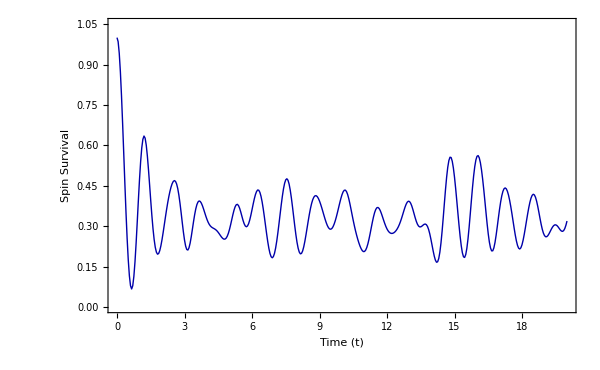

```mathematica
(* 2. Zip it with your time list so you can plot it *)
spinSurvivalData = Transpose[{tlist, spinSurvivalList}];
(* 3. Plot the result *)
ListLinePlot[spinSurvivalData,
 PlotRange -> {0, 1.05},
 Frame -> True,
 FrameLabel -> {"Time (t)", "Spin Survival"},
LabelStyle->Directive[Black,20],
 PlotStyle -> {Thick, Darker[Blue]},
ImageSize->600
]
```

```mathematica
ClearAll[Concurrence]
Concurrence[rho_] := Module[{sigmaY, spinFlip, rhoTilde, RmatrixEvals, lambdas},
  (* 1. Define the global spin-flip operator *)
  sigmaY = PauliMatrix[2];
  spinFlip = KroneckerProduct[sigmaY, sigmaY];
    (* 2. Calculate the spin-flipped density matrix *)
  (* Note: Conjugate applies complex conjugation to the matrix elements *)
  rhoTilde = spinFlip . Conjugate[rho] . spinFlip;
    (* 3. Find the eigenvalues of the product rho . rhoTilde *)
  RmatrixEvals = Chop[Eigenvalues[rho . rhoTilde]];
    (* 4. Take the square roots and sort them from largest to smallest *)
  (* We use Re[] to strip any microscopic imaginary numerical artifacts *)
  lambdas = Reverse[Sort[Re[Sqrt[RmatrixEvals]]]];
    (* 5. Apply the Wootters formula *)
  Max[0, lambdas[[1]] - lambdas[[2]] - lambdas[[3]] - lambdas[[4]]]
];
```

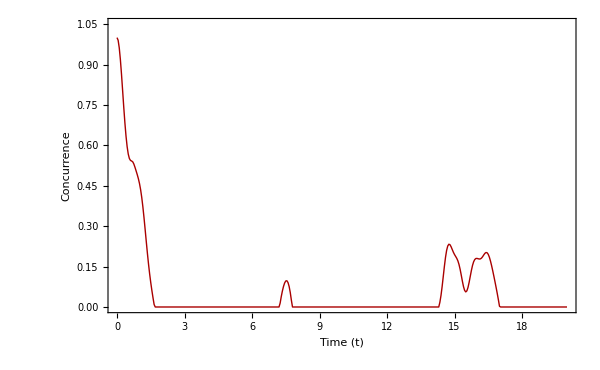

```mathematica
(* Calculate Concurrence for all 501 time steps *)
concurrenceList = Concurrence /@ rhoevolved;

(* Zip with your time list for plotting *)
concurrenceData = Transpose[{tlist, concurrenceList}];

(* Plot Concurrence to see the exact moment entanglement dies *)
ListLinePlot[concurrenceData,
 PlotRange -> {0, 1.05},
 Frame -> True,
 FrameLabel -> {"Time (t)", "Concurrence"},
LabelStyle->Directive[Black,20],
 PlotStyle -> {Thick, Darker[Red]},
ImageSize->600
]
```

## All measures

```mathematica
(* ========================================== *)
(* 1. DEFINE FAST ENTROPY AND TRACE FUNCTIONS *)
(* ========================================== *)
ClearAll[VNEntropy, TraceOutQubit2, TraceOutQubit1]

(* Safely computes Von Neumann entropy for any density matrix *)
VNEntropy[rho_] := Module[{evals},
  (* Extract strictly positive eigenvalues to avoid Log[0] errors *)
  evals = Select[Re[Chop[Eigenvalues[rho]]], # > 10^-10 &];
  Total[-evals*Log[evals]]
]
(* Fast manual partial trace to get Spin 1 (traces out Spin 2) *)
TraceOutQubit2[rho_] := {
  {rho[[1, 1]] + rho[[2, 2]], rho[[1, 3]] + rho[[2, 4]]},
  {rho[[3, 1]] + rho[[4, 2]], rho[[3, 3]] + rho[[4, 4]]}
}
(* Fast manual partial trace to get Spin 2 (traces out Spin 1) *)
TraceOutQubit1[rho_] := {
  {rho[[1, 1]] + rho[[3, 3]], rho[[1, 2]] + rho[[3, 4]]},
  {rho[[2, 1]] + rho[[4, 3]], rho[[2, 2]] + rho[[4, 4]]}
}
```

```mathematica
(* ========================================== *)
(* 2. COMPUTE ALL METRICS ACROSS TIME         *)
(* ========================================== *)

(* Survival Probability and Concurrence (using your existing functions) *)
spinSurvivalList = SurvivalProbability[rho12, #] & /@ rhoevolved;
concurrenceList = Concurrence /@ rhoevolved;
(* Purity of the joint 4x4 state: Tr(rho^2) *)
purityList = Re[Chop[Tr[# . #]]] & /@ rhoevolved;
(* Von Neumann Entropy of just Spin 1 *)
rhoSpin1List = TraceOutQubit2 /@ rhoevolved;
entropySpin1List = VNEntropy /@ rhoSpin1List;
(* Mutual Information: Total correlations (Classical + Quantum) *)
(* I(A:B) = S(A) + S(B) - S(AB) *)
rhoSpin2List = TraceOutQubit1 /@ rhoevolved;
mutualInfoList = Table[
  VNEntropy[rhoSpin1List[[i]]] + VNEntropy[rhoSpin2List[[i]]] - VNEntropy[rhoevolved[[i]]],
  {i, Length[rhoevolved]}
];
```

```mathematica
(* ========================================== *)
(* 3. ZIP DATA WITH TIME LIST FOR PLOTTING    *)
(* ========================================== *)
dataSurvival = Transpose[{tlist, spinSurvivalList}];
dataConcurrence = Transpose[{tlist, concurrenceList}];
dataPurity = Transpose[{tlist, purityList}];
dataEntropy1 = Transpose[{tlist, entropySpin1List}];
dataMutualInfo = Transpose[{tlist, mutualInfoList}];
```

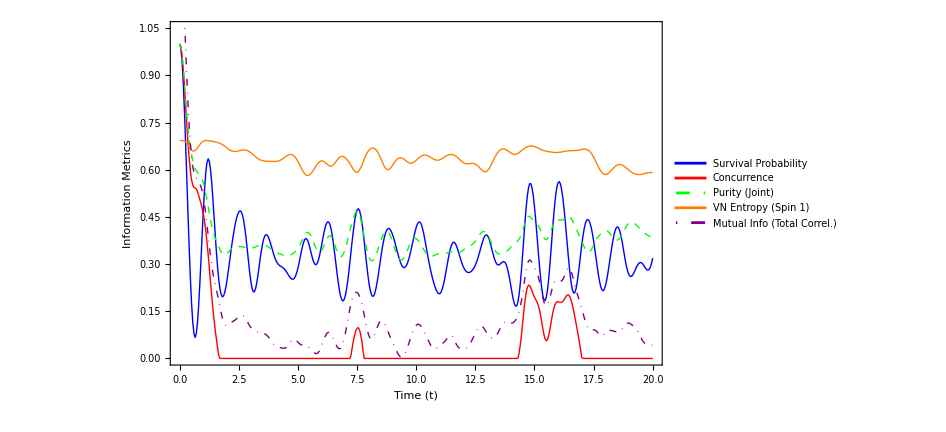

```mathematica
(* ========================================== *)
(* 4. THE UNIFIED MULTI-PLOT                  *)
(* ========================================== *)
ListLinePlot[
  {dataSurvival, dataConcurrence, dataPurity, dataEntropy1, dataMutualInfo},
  PlotRange -> {0, 1.05},
  Frame -> True,
  FrameLabel -> {"Time (t)", "Information Metrics"},
  LabelStyle -> Directive[Black, 16],
  ImageSize -> 700,
  PlotStyle -> {
    Directive[Thick, Blue],               (* Survival *)
    Directive[Thick, Red],                (* Concurrence *)
    Directive[Thick, Green, Dashed],      (* Purity *)
    Directive[Thick, Orange],             (* Entropy Spin 1 *)
    Directive[Thick, Purple, DotDashed]   (* Mutual Info *)
  },
  PlotLegends -> Placed[
    LineLegend[
      {"Survival Probability", "Concurrence", "Purity (Joint)", "VN Entropy (Spin 1)", "Mutual Info (Total Correl.)"},
      LegendFunction -> Framed
    ], 
    Right
  ]
]
```

# Spin chain XXZ generalizing

## Setup

```mathematica
L=5;
```

```mathematica
(*Spin 1*)
H1[Δa_]:=Δa*Pauli[3];
(*Spin 2*)
H2[Δb_]:=Δb*Pauli[3];
Pauliplus=PauliMatrix[1]+I*PauliMatrix[2];
Pauliminus=PauliMatrix[1]-I*PauliMatrix[2];
```

```mathematica
(*Spin 1 coupling*)
H1c[λa_]:=λa*(KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]+ConjugateTranspose[KroneckerProduct[Pauliplus,KroneckerProduct[Pauliminus,IdentityMatrix[2^(L-1)]],IdentityMatrix[2]]]);
(*Spin 2*)
H2c[λb_]:=λb*(KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]+ConjugateTranspose[KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2^(L-1)],Pauliplus],Pauliminus]]);
```

```mathematica
ClearAll[DensityMatrixEvolution];
DensityMatrixEvolution[t_, rho0_, eigenvals_, eigenvecs_] := 
 Module[{rhoEnergy, phaseMatrix, rhoEnergyT},
rhoEnergy = eigenvecs . rho0 . ConjugateTranspose[eigenvecs];
phaseMatrix = Table[Exp[-I * (m - n) * t], {m, eigenvals}, {n, eigenvals}];
rhoEnergyT = rhoEnergy * phaseMatrix;
Chop[ConjugateTranspose[eigenvecs].rhoEnergyT.eigenvecs]
]
```

```mathematica
ClearAll[Survivalrho]
Survivalrho[rho0_, rhot_] := Module[{sqrtRho0},
  (* Check if rho0 is pure to use the faster standard trace method *)
  If[Chop[Tr[rho0 . rho0]] >= 0.999,
   Chop[Tr[rho0 . rhot]], 
   (* Otherwise, use the full mixed-state Uhlmann fidelity definition *)
   sqrtRho0 = MatrixPower[rho0, 1/2];
   Chop[Tr[MatrixPower[sqrtRho0 . rhot . sqrtRho0, 1/2]]]^2
  ]
]
```

```mathematica
ClearAll[VNentropy]
VNentropy[0 | 0.] = 0;
VNentropy[x_] := -x*Log[x];
```

## Parameters

```mathematica
?OpenXXZHamiltonian
```

```mathematica
Δ=5.;
h1=0.9;
h2=1.1;
```

```mathematica
Ha=OpenXXZHamiltonian[L,Δ,h1,h2];
```

```mathematica
Clear[Hlocal];
Hlocal[Δa_,Δb_]:=KroneckerProduct[H1[Δa],IdentityMatrix[2^L],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],Ha,IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2^L],H2[Δb]];
```

```mathematica
Clear[HT];
HT[Δa_,Δb_,λa_,λb_]:=Hlocal[Δa,Δb]+H1c[λa]+H2c[λb];
```

```mathematica
(* 1. Setup states exactly as you have them *)
bellState = 1/Sqrt[2]*{1, 0, 0, 1};
rho12 = Dyad[bellState];
rhochain = Dyad[coherentstate[qubit[0., 0], L]];
rhochain = Dyad[RandomChainProductState[L]];
tempInitial = KroneckerProduct[rho12, rhochain];
```

```mathematica
(* Layout of tempInitial is [Q1, Q2, Chain] *)
dimC = 2^L;
(* but calculate the position of that state in the old [q1, q2, c] layout *)
permList = Flatten[Table[
    q1 * (2^(L + 1)) + q2 * (2^L) + c + 1, 
    {q1, 0, 1}, {c, 0, dimC - 1}, {q2, 0, 1}
]];
(* Transform the general matrix into your physical layout [Q1, Chain, Q2] *)
initial = tempInitial[[permList, permList]];
```

```mathematica
initialchain=RandomChainProductState[L];
initialspin1=RandomChainProductState[0];
initialspin2=RandomChainProductState[1];
initial=Flatten[KroneckerProduct[initialspin1,initialchain,initialspin2]];
initial=Dyad[initial];
```

## Method

```mathematica
{Δa,Δb,λa,λb}={1,1,0.35,0.35};
```

```mathematica
{fullval,fullvec}=Transpose[Sort[Transpose[Eigensystem[HT[Δa,Δb,λa,λb]]]]];
```

```mathematica
MeanLevelSpacingRatio[Sort[fullval]]
```

0.332876

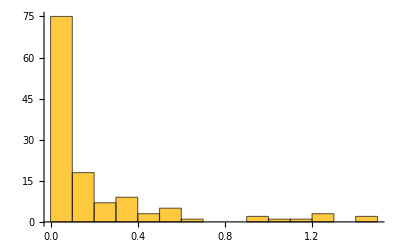

```mathematica
Histogram[Differences[Sort[fullval]],PlotRange->All]
```

```mathematica
tlist=Table[i,{i,0,20,0.05}];
```

```mathematica
(* Run the full matrix evolution loop *)
globalEvolutionData = ParallelTable[
   Module[{rhoGlobal, surv,rhoReduced},
rhoGlobal=DensityMatrixEvolution[t, initial,fullval,fullvec];
   (* 2. Compute global survival probability *)
    surv = Survivalrho[initial, rhoGlobal];    
    (* 3. Compute the reduced 4x4 density matrix for your spins *)
    rhoReduced = Chop[MatrixPartialTrace[rhoGlobal, {2}, {2, 2^L, 2}]];    
    (* Return everything in a structured association for easy access *)
    <|"Time" -> t, "Survival" -> surv, "RhoReduced" -> rhoReduced|>
   ],
   {t, tlist},
   DistributedContexts -> Full
];
```

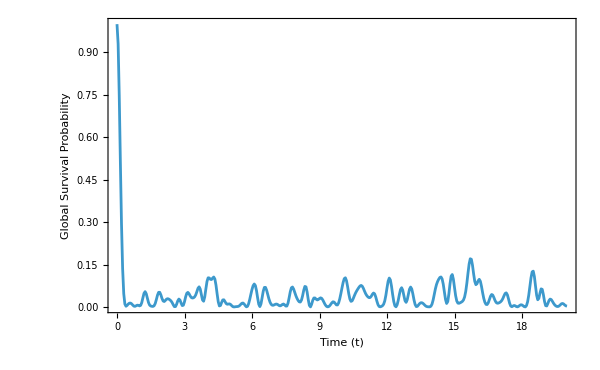

```mathematica
ListLinePlot[Table[{d["Time"],d["Survival"]},{d,globalEvolutionData}],PlotRange->All,Frame->True,FrameLabel->{"Time (t)","Global Survival Probability"},ImageSize->600]
```

## Subsystem evolution

```mathematica
(* Evolve the full density matrix and isolate ONLY Spin 1 *)
rhoevolved = ParallelTable[
     Module[{rhoGlobal},
rhoGlobal = DensityMatrixEvolution[t, initial, fullval, fullvec];Chop[MatrixPartialTrace[rhoGlobal, {2, 3}, {2, 2^L, 2}]]
     ], 
     {t, tlist}, 
     DistributedContexts -> Full
   ];
```

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,rhoevolved}];
```

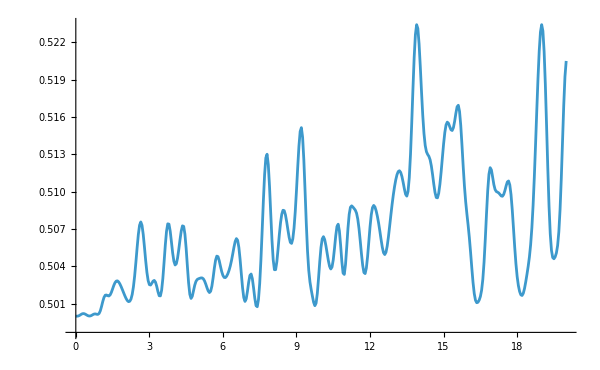

```mathematica
ListPlot[Transpose[{tlist,purity}],PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
(* Calculate entropy for every time step *)
entropyList = Table[Total[VNentropy /@ Chop[Eigenvalues[rho]]],{rho, rhoevolved}];
```

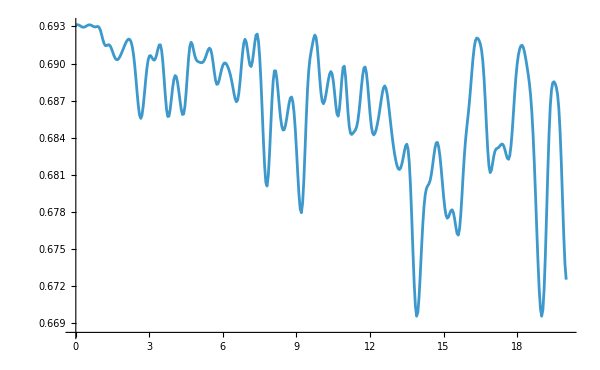

```mathematica
ListPlot[Transpose[{tlist,entropyList}],PlotRange->All,Joined->True,ImageSize->600]
```

```mathematica
(* Ensure the function is defined just in case *)
ClearAll[SurvivalProbability]
SurvivalProbability[rho0_, rhot_] := Module[{sqrtRho0},
  (* Check if rho0 is pure to use the faster standard trace method *)
  If[Chop[Tr[rho0 . rho0]] >= 0.999,
   Chop[Tr[rho0 . rhot]], 
   (* Otherwise, use the full mixed-state Uhlmann fidelity definition *)
   sqrtRho0 = MatrixPower[rho0, 1/2];
   Chop[Tr[MatrixPower[sqrtRho0 . rhot . sqrtRho0, 1/2]]]^2
  ]
]
```

```mathematica
(* Evolve the full density matrix and isolate ONLY Spin 1 *)
rhoevolved = ParallelTable[
     Module[{rhoGlobal},
rhoGlobal = DensityMatrixEvolution[t, initial, fullval, fullvec];Chop[MatrixPartialTrace[rhoGlobal, {2}, {2, 2^L, 2}]]
     ], 
     {t, tlist}, 
     DistributedContexts -> Full
   ];
```

```mathematica
(* 1. Calculate the survival probability of the 2-qubit state over time *)
spinSurvivalList = Table[
   SurvivalProbability[rho12, rhot], 
   {rhot, rhoevolved}
];
```

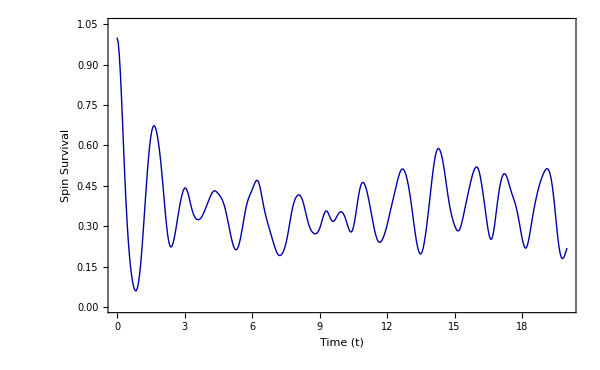

```mathematica
(* 2. Zip it with your time list so you can plot it *)
spinSurvivalData = Transpose[{tlist, spinSurvivalList}];
(* 3. Plot the result *)
ListLinePlot[spinSurvivalData,
 PlotRange -> {0, 1.05},
 Frame -> True,
 FrameLabel -> {"Time (t)", "Spin Survival"},
LabelStyle->Directive[Black,20],
 PlotStyle -> {Thick, Darker[Blue]},
ImageSize->600
]
```

```mathematica
ClearAll[Concurrence]
Concurrence[rho_] := Module[{sigmaY, spinFlip, rhoTilde, RmatrixEvals, lambdas},
  (* 1. Define the global spin-flip operator *)
  sigmaY = PauliMatrix[2];
  spinFlip = KroneckerProduct[sigmaY, sigmaY];
    (* 2. Calculate the spin-flipped density matrix *)
  (* Note: Conjugate applies complex conjugation to the matrix elements *)
  rhoTilde = spinFlip . Conjugate[rho] . spinFlip;
    (* 3. Find the eigenvalues of the product rho . rhoTilde *)
  RmatrixEvals = Chop[Eigenvalues[rho . rhoTilde]];
    (* 4. Take the square roots and sort them from largest to smallest *)
  (* We use Re[] to strip any microscopic imaginary numerical artifacts *)
  lambdas = Reverse[Sort[Re[Sqrt[RmatrixEvals]]]];
    (* 5. Apply the Wootters formula *)
  Max[0, lambdas[[1]] - lambdas[[2]] - lambdas[[3]] - lambdas[[4]]]
];
```

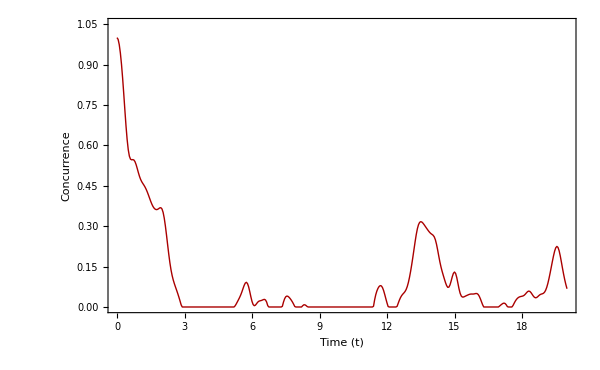

```mathematica
(* Calculate Concurrence for all 501 time steps *)
concurrenceList = Concurrence /@ rhoevolved;

(* Zip with your time list for plotting *)
concurrenceData = Transpose[{tlist, concurrenceList}];

(* Plot Concurrence to see the exact moment entanglement dies *)
ListLinePlot[concurrenceData,
 PlotRange -> {0, 1.05},
 Frame -> True,
 FrameLabel -> {"Time (t)", "Concurrence"},
LabelStyle->Directive[Black,20],
 PlotStyle -> {Thick, Darker[Red]},
ImageSize->600
]
```

## All measures

```mathematica
(* ========================================== *)
(* 1. DEFINE FAST ENTROPY AND TRACE FUNCTIONS *)
(* ========================================== *)
ClearAll[VNEntropy, TraceOutQubit2, TraceOutQubit1]

(* Safely computes Von Neumann entropy for any density matrix *)
VNEntropy[rho_] := Module[{evals},
  (* Extract strictly positive eigenvalues to avoid Log[0] errors *)
  evals = Select[Re[Chop[Eigenvalues[rho]]], # > 10^-10 &];
  Total[-evals*Log[evals]]
]
(* Fast manual partial trace to get Spin 1 (traces out Spin 2) *)
TraceOutQubit2[rho_] := {
  {rho[[1, 1]] + rho[[2, 2]], rho[[1, 3]] + rho[[2, 4]]},
  {rho[[3, 1]] + rho[[4, 2]], rho[[3, 3]] + rho[[4, 4]]}
}
(* Fast manual partial trace to get Spin 2 (traces out Spin 1) *)
TraceOutQubit1[rho_] := {
  {rho[[1, 1]] + rho[[3, 3]], rho[[1, 2]] + rho[[3, 4]]},
  {rho[[2, 1]] + rho[[4, 3]], rho[[2, 2]] + rho[[4, 4]]}
}
```

```mathematica
(* ========================================== *)
(* 2. COMPUTE ALL METRICS ACROSS TIME         *)
(* ========================================== *)

(* Survival Probability and Concurrence (using your existing functions) *)
spinSurvivalList = SurvivalProbability[rho12, #] & /@ rhoevolved;
concurrenceList = Concurrence /@ rhoevolved;
(* Purity of the joint 4x4 state: Tr(rho^2) *)
purityList = Re[Chop[Tr[# . #]]] & /@ rhoevolved;
(* Von Neumann Entropy of just Spin 1 *)
rhoSpin1List = TraceOutQubit2 /@ rhoevolved;
entropySpin1List = VNEntropy /@ rhoSpin1List;
(* Mutual Information: Total correlations (Classical + Quantum) *)
(* I(A:B) = S(A) + S(B) - S(AB) *)
rhoSpin2List = TraceOutQubit1 /@ rhoevolved;
mutualInfoList = Table[
  VNEntropy[rhoSpin1List[[i]]] + VNEntropy[rhoSpin2List[[i]]] - VNEntropy[rhoevolved[[i]]],
  {i, Length[rhoevolved]}
];
```

```mathematica
(* ========================================== *)
(* 3. ZIP DATA WITH TIME LIST FOR PLOTTING    *)
(* ========================================== *)
dataSurvival = Transpose[{tlist, spinSurvivalList}];
dataConcurrence = Transpose[{tlist, concurrenceList}];
dataPurity = Transpose[{tlist, purityList}];
dataEntropy1 = Transpose[{tlist, entropySpin1List}];
dataMutualInfo = Transpose[{tlist, mutualInfoList}];
```

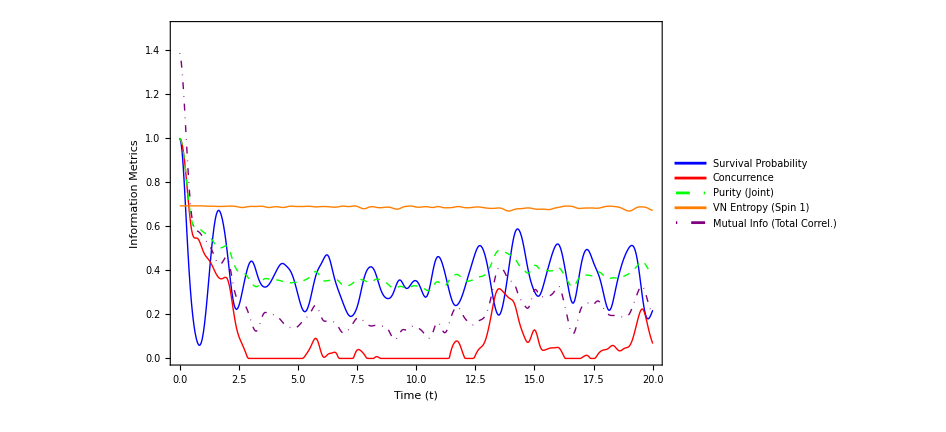

```mathematica
(* ========================================== *)
(* 4. THE UNIFIED MULTI-PLOT                  *)
(* ========================================== *)
ListLinePlot[
  {dataSurvival, dataConcurrence, dataPurity, dataEntropy1, dataMutualInfo},
  PlotRange -> {0, 1.5},
  Frame -> True,
  FrameLabel -> {"Time (t)", "Information Metrics"},
  LabelStyle -> Directive[Black, 16],
  ImageSize -> 700,
  PlotStyle -> {
    Directive[Thick, Blue],               (* Survival *)
    Directive[Thick, Red],                (* Concurrence *)
    Directive[Thick, Green, Dashed],      (* Purity *)
    Directive[Thick, Orange],             (* Entropy Spin 1 *)
    Directive[Thick, Purple, DotDashed]   (* Mutual Info *)
  },
  PlotLegends -> Placed[
    LineLegend[
      {"Survival Probability", "Concurrence", "Purity (Joint)", "VN Entropy (Spin 1)", "Mutual Info (Total Correl.)"},
      LegendFunction -> Framed
    ], 
    Right
  ]
]
```